-Graphics-

Bienvenidos a mmAeScience!
https://github.com/josemramirez/mmaescience /QM_intro-[for MMaTeX]_beta^v14

# eScience - Habla Mecánica Cuántica!

Funciones:

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"QMfunctions_v1.nb"];
```

```mathematica
Siguiendo la segunda edición de David J Griffiths, Reed College.
por JM Ramírez, 2024.
```

```mathematica
PARTE I Teoría
```

◀ prev - + prox ▶

e Guardar
d Resetear

## Método algebraico

```mathematica
Reescribamos
```

1/(2 m)[p^2+(mωx)^2]ψ=Eψ      (2.45)

```mathematica
Si fueran números... u^2+v^2=(v+iu)(v-iu) .... ¡El problema es! que no son (son operadores). En otras palabras, no CONMUTAN.
```

```mathematica
Tomemos lo que sería:
```

a_±=1/(√(2ℏmω))[∓ip+mωx]     (2.47)

```mathematica
Y compruebe la operación SubMinus[a] SubPlus[a]
```

```mathematica
Remove["Global`*"]
```

```mathematica
Needs["Quantum`Notation`"];
```

```mathematica
SetQuantumObject[x, p];
```

```mathematica
(* == Una expansion no Conmutativa == *)
Expand[(a+b)^2]
Expand[(x+p)^2]
(*⟦x,p⟧_-
EvaluateCommutators[⟦x,p⟧_-]*)
```

```mathematica
ap=1/Sqrt[2ℏ m ω](-I p+m ω x)
am=1/Sqrt[2ℏ m ω](+I p+m ω x)
CommutatorExpand[(-I p+m ω x)^2](*//Collect[#,1/Sqrt[2ℏ m ω]]&*)
(* Not perfect yet!! ==*)
```

(-ⅈ p+m x ω)/(√2 √(m ω ℏ))

(ⅈ p+m x ω)/(√2 √(m ω ℏ))

-p^2+m^2 x^2 ω^2-ⅈ m ω p·x-ⅈ m ω (-⟦p,x⟧_-+p·x)

```mathematica
Bueno, ¿cúal es el producto SubMinus[a] SubPlus[a]?
```

a_-a_+=1/(2ℏmω) [p^2+(mωx)^2-ⅈmω(xp-px),

Hay un término extra, que involucra (xp-px).

```mathematica
[A,B] ≡ AB - BA (2.48)
```

En esta notación

a_-a_+=1/(2ℏmω) [p^2+(mωx)^2]-ⅈ/(2ℏ)[x,p], (2.49)

```mathematica
(véase 2.50).
```

```mathematica
[x,p]=ⅈħ.     (2.51)
```

```mathematica
Este resultado encantador y ubicuo se conoce como la relación de conmutación canónica.
```

Con este

[a_-,a_+]=1     (2.55)

```mathematica
y
```

H = ℏω (a_+ a_- + 1/2).   (2.56)

Así que la ecuación de Schrödinger para el oscilador armónico toma la forma

ℏω (a_± a_∓ ± 1/2)ψ=Eψ.   (2.57)

```mathematica
David afirma que: si ψ satisface la ecuación de Schrödinger con energía E, entonces SubPlus[a]ψ satisface la ecuación de Schrödinger con energía (E+ħω). (si se prueba el tiempo en el aula)
```

```mathematica
Del mismo modo, si ψ satisface la ecuación de Schrödinger con Energía E, entonces SubMinus[a]ψ satisface la ecuación de Schrödinger con Energía (E-ħω). Aquí, entonces, una máquina maravillosa para generar nuevas soluciones.
```

¡Si pudiéramos encontrar una solución, para empezar! Los llamamos operadores de escaleras, porque nos permiten subir y bajar de energía. a_+ es el operador de subida y a_- el operador de bajada.

Se produce un "peldaño más bajo" (llámalo ψ_0) tal que

a_-ψ_0 = 0.   (2.58)

```mathematica
Muy fácil de resolver
```

ψ_0(x)=AExp(-mω/(2ℏ)x^2).

con A^2= Sqrt[mω/πħ].

Ver

```mathematica
(* == Important for the normalization == *)
Integrate[Exp[-x^2],x]
Limit[Erf[x],x->-Infinity]
Limit[Erf[x],x->Infinity]
```

1/2 √π Erf[x]

-1

1

```mathematica
Uso de (2.57)
```

E_0=1/2ℏω.    (2.60)

```mathematica
Con el pie ahora firmemente plantado en el peldaño inferior (el estado fundamental del oscilador cuántico):
```

ψ_n(x)=A_n(a_+)^n ψ_0(x), with E_n=(n+1/2)ℏω,   (2.61)

```mathematica
Ejemplos y problemas ...
```

## Método numérico de los operadores de escalera

```mathematica
<< Notation`
```

```mathematica
Symbolize[a_+]
Symbolize[a_-]
```

```mathematica
Symbolize[x̂]
Symbolize[p̂]
```

```mathematica
x̂[f_]:= (SubPlus[a][f]+SubMinus[a][f])/2
p̂[f_]:= (SubMinus[a][f]-SubMinus[a][f])/(2 ⅈ)
```

```mathematica
SubPlus[a][f_]:=Simplify[-D[f,q]+q  f]
SubMinus[a][f_]:=Simplify[D[f,q]+q  f]
ψ0=(1/√π)^(1/2)Exp[-q^2/2];
ψ[n_,q_]:=Nest[SubPlus[a],ψ0,n]/Product[√(2(i+1)),{i,0,n-1}]
```

```mathematica
ψ[2, q]
```

(ⅇ^(-q^2/2) (-2+4 q^2))/(2 √2 π^(1/4))

## Método analítico

Volvemos ahora a la ecuación de Schrödinger para el oscilador armónico,

-ℏ^2/(2m)(d^2 ψ)/dx^2+1/2 m ω^2 x^2=E ψ .  (2.70)

Introduzca la variable adimensional ξ=√(mω/ℏ)x (2.71)

(d^2 ψ)/dξ^2=(ξ^2-K) ψ .  (2.72)

```mathematica
donde K ≡ (2E)/ħω (2.73)
```

```mathematica
Con ξ muy grande
```

(d^2 ψ)/dξ^2≈ξ^2 ψ ,  (2.74)

que tiene solución

ψ(ξ)≈AExp(-ξ^2/2)+BExp(+ξ^2/2).   (2.75)

```mathematica
Claramente, físicamente
```

ψ(ξ)=h(ξ)Exp(-ξ^2/2),   (2.77)

```mathematica
Diferenciar dos veces
```

```mathematica
La ecuación de Schrödinger (2.72) se convierte (en términos de h):
```

(d^2 h)/dξ^2-2ξ dh/dξ(K-1)h=0 .  (2.78)

```mathematica
Tiene solución en forma de serie de potencia en ξ !
```

h(ξ)=a_0 +a_1ξ+a_2 ξ^2+  ... = ∑_(j=0)^∞ a_j ξ^j   (2.79)

### ¡Comprobación rápida!

4.+2.1 x^2+1.2 x^3

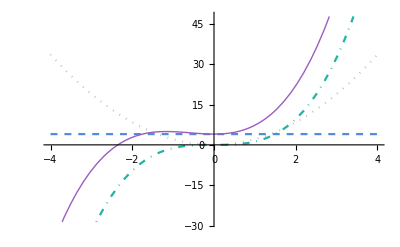

```mathematica
hf1=4.;hf2=2.1x^2;hf3=1.2x^3;
hfunction1=hf1+hf2+hf3
Plot[{hf1,hf2,hf3,hfunction1},{x,-4,4},PlotStyle->{{Dashed},{Dotted},{DotDashed},{Thick}}]
```

```mathematica
Diferenciar dos veces
```

```mathematica
hfunction1=Sum[Subscript[a, j] ξ^j,{j,0,5}];
dhfunction1=D[hfunction1,ξ]
dhfunction2=D[dhfunction1,ξ]
```

a_1+2 ξ a_2+3 ξ^2 a_3+4 ξ^3 a_4+5 ξ^4 a_5

2 a_2+6 ξ a_3+12 ξ^2 a_4+20 ξ^3 a_5

{{1,ξ a_1},{2,ξ^2 a_2},{3,ξ^3 a_3}}

```mathematica
Poniéndolos en la ecuación (2.78)
```

∑_(j=0)^∞ [((j+1)(j+2)a)_(j+2) -2j a_j+(K-1)a_j]ξ^j=0   (2.80)

```mathematica
Cada potencia de ξ debe desaparecer,
```

```mathematica
CoefRecur1=(j+1)(j+2)Subscript[a, j+2] -2j Subscript[a, j]+(K1-1)Subscript[a, j]==0
RecursionFormula=Solve[CoefRecur1,Subscript[a, j+2]]
```

-2 j a_j+(-1+K1) a_j+(1+j) (2+j) a_(2+j)==0

{{a_(2+j)→(a_j+2 j a_j-K1 a_j)/((1+j) (2+j))}}

-2 j a_j+(-1+K1) a_j+(1+j) (2+j) a_(2+j)==0

{{a_(2+j)→(a_j+2 j a_j-K1 a_j)/((1+j) (2+j))}}

```mathematica
Esta fórmula de recursividad es totalmente equivalente a la ecuación de Schrödinger. Escribimos la solución completa como
```

h(ξ)=Subíndice[h, par](ξ) + Subíndice[h, impar] (ξ), (2.82)

Ecuación diferencial de segundo orden -> 2 constantes (a_0 y a_1).

```mathematica
En el caso de las soluciones normalizables, la serie de potencias debe terminar. Debe ocurrir alguna j más alta (llamada n) tal que la fórmula de recursividad escupe Subscript[a, n+2] = 0.
```

Por lo tanto, para una solución físicamente aceptable

```mathematica
K11=2n+1;
K11=2 Subscript[Ene, n]/(ℏ ω);
SolK=2 Subscript[Ene, n]/(ℏ ω)==2n+1;
(* For n=0,1,2,...*)
Solve[SolK,Subscript[Ene, n]]
```

{{Ene_n→1/2 (1+2 n) ω ℏ}}

Por lo tanto, recuperamos, por un método completamente diferente, la condición de cuantización fundamental que encontramos algebraicamente en la ecuación 2.61.

Para los valores permitidos de K, la fórmula de recursividad dice

```mathematica
Clear[K1]
```

```mathematica
Collect[RecursionFormula[[1,1,2]]/.{K1->2n+1},Subscript[a, j]]
```

((2 j-2 n) a_j)/((1+j) (2+j))

```mathematica
En general, el Subscript[h, n](ξ) será un grado polinómico n en ξ que involucra potencia par si n es par e impares si n es impar. Aparte de los (a0 y a1) son los llamados polinomios de Hermite Subscript[H, n](ξ).
```

```mathematica
HermiteH[5, x]
```

120 x-160 x^3+32 x^5

```mathematica
Con esto, los estados estacionarios normalizados para el oscilador armónico son
```

ψ_n(x)=(mω/πℏ)^(1/4) 1/(√(2^n n!))H_n(ξ) e^(-ξ^2/2) .  (2.85)

```mathematica
¡Bien!
```

## Representación gráfica de la Figura 2.7:

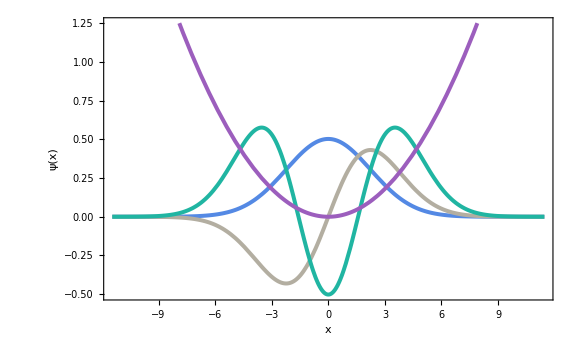

```mathematica
(* == Wait for the explanation, but this is it! ==*)
ψ[n_,ω_,x_]:=(ω/π)^(1/4)/(√(2^n n!))ⅇ^(-ω x^2/2) HermiteH[n,√ω x]
(* == Ladder operators ==, a es cuantos escalones quieres moverte *)
g[n_,ω_,a_]:=√(n+a) ψ[n+2a-1,ω,x]
(* === Plotting the solution === *)
Plot[{ψ[0,0.2,x],g[0,0.2,1],g[1,0.2,1],
(* == The potential ==*)
1/2((0.2)^2x^2)},
{x,-4 √((2+1)/(2*0.2))-.5,4 √((2+1)/(2*0.2))+.5},
Frame->True,
PlotStyle->{Thickness@0.005},
LabelStyle->Directive[Black,25],
FrameLabel->{Style["x",24],Style["ψ(x)",24]
,Style["Fig. 2.7: The first three states",24]},
FrameTicks->None,
ImageSize->Large]
```

Vea si hay tiempo para 2.15, 2.16 y 2.17.

## Problema 2.54: El método Wag-the-dog

```mathematica
Clear[u, x]
```

```mathematica
(* == From the Griffiths itfself, Problem 2.54, page 92 ==*)
a=-10;b=10;c=-10;d=10;
(* == The Trial value here ==*)
(*K1=0.9;*)
K1=1.0;
EqWag1=u''[x]-(x^2-K1)u[x]==0;
EqWag1Sol=NDSolve[{EqWag1,u[0]==1.0,u'[0]==0.},
u,{x,-10,10},MaxSteps->2000]
```

{{u→InterpolatingFunction[{{-10., 10.}}, <>]}}

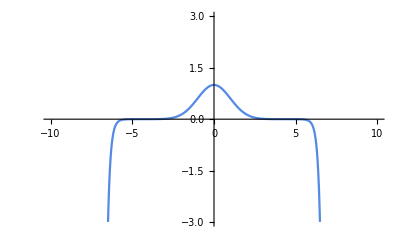

```mathematica
Plot[Evaluate[u[x] /. EqWag1Sol], {x, a, b}, PlotRange -> {-3, 3}]
```

La partícula libre

-ℏ^2/(2m)(d^2 ψ)/dx^2 = Eψ,   (2.90) 
or
(d^2 ψ)/dx^2=-k^2ψ,   with  k= (2mE)^(1/2)/ℏ   (2.91)

```mathematica
EqFree1 = schroedingerD[0][psi[x]] == 0
```

-Energy psi[x]-(ℏ^2 psi''[x])/(2 m)==0

```mathematica
DSolve[EqFree1, psi, x]
```

{{psi→Function[{x},C[1] Cos[(√2 √Energy √m x)/ℏ]+C[2] Sin[(√2 √Energy √m x)/ℏ]]}}

```mathematica
Escribamos en términos de exponenciales
```

```mathematica
ψ(x)=Aⅇ^(+ⅈκx)+Bⅇ^-ⅈκx.   (2.92)
```

No hay condiciones de contorno que restrinjan el posible valor de κ (y, por lo tanto, de E); La partícula libre puede transportar cualquier energía positiva. Añadiendo la dependencia de la hora estándar,

Ψ(x,t)=Aⅇ^(ⅈκ(x-ℏκ/(2m)t))+Bⅇ^(-ⅈκ(x+ℏκ/(2m)t)).   (2.93)

```mathematica
Ahora, cualquier función de x y t que dependa de (x±vt): REPRESENTA una onda de perfil fijo, que viaja en la dirección ∓ x, a velocidad v.
```

```mathematica
x = ∓ vt + C
```

Dado que todos los puntos de la forma de onda se mueven con la misma velocidad, su forma no cambia a medida que se propaga. Mejor

Ψ(x,t)=Aⅇ^(ⅈ(κx-ℏκ^2/(2m)t)),   
with k = ± (2mE)^(1/2)/ℏ, 
k>0 traveling right and 
k<0 traveling left    (2.95)

```mathematica
Evidentemente los estados estacionarios de la partícula libre son ondas que se propagan; la onda es λ=2π/|κ|, y de acuerdo con la fórmula de Broglie, llevan momento
```

```mathematica
p = ħκ (2.96)
```

```mathematica
La velocidad de estas ondas (el coeficiente t sobre el de x) es
```

v_quantum = (ℏ|κ|)/(2m)= √(E/(2m))   (2.97)

```mathematica
Por otro lado, clásicamente, E=1/2 mv^2.
```

v_classical = 2v_quantum  (2.98)

¿A medias?, ¿Una paradoja?

```mathematica
¡No es normalizable!
```

```mathematica
No existe tal cosa como una partícula libre con una energía definida.
```

Ψ(x,t)=1/(√(2π))∫_(-∞)^(+∞) ϕ(k)ⅇ^(ⅈ(kx-ℏk^2/(2m)t))ⅆk.   (2.100)

```mathematica
Subscript[c, n] ->  1/(√(2π))ϕ(k)dk. Ahora bien, esta función de onda puede ser normalizable (para φ(k)). Pero necesariamente lleva un rango de k y, por lo tanto, de energías y velocidades. ¡Lo llamamos un paquete de onda!.
```

El teorema de Plancherel

f(x)=1/(√(2π))∫_(-∞)^(+∞) F(k)ⅇ^ⅈkx ⅆk   
< --- >    F(k)=1/(√(2π))∫_(-∞)^(+∞) f(x)ⅇ^-ⅈkx ⅆx    (2.102)

```mathematica
F(k) se llama la transformada de Fourier de f(x); f(x) es la transformada inversa de Fourier de F(k).
```

```mathematica
Así que la solución al problema cuántico genérico para la partícula libre es,
```

ϕ(k)=1/(√(2π))∫_(-∞)^(+∞) Ψ(x,0)ⅇ^-ⅈkx ⅆx .   (2.103)

## Ejemplo 2.6

```mathematica
En t=0:
```

```mathematica
Ψx0[x_] := Piecewise[{{A, -a <= x <= a}, {0, True}}]
```

```mathematica
Solución: Primero necesitamos normalizar Ψ(x,0):
```

```mathematica
(* == The Assumptions is key !! == nice to do it like that ==*)
Integrate[(Ψx0[x])^2,{x,-a,a},Assumptions->{x∈Reals, a∈Reals}]
```

Piecewise[{{2 a A^2, a>0}, {0, True}}]

```mathematica
NormaEx26=A^2 Integrate[1,{x,-a,a},Assumptions->{x∈Reals, a∈Reals}]==1
NormSol26a=Solve[NormaEx26,A][[2]][[1]][[2]](* We assume is positive *)
```

2 a A^2==1

1/(√2 √a)

```mathematica
A continuación, calculamos φ(k) usando 2.103
```

Remember ⅇ^ⅈθ=cosθ+ⅈsinθ 
(keep this, ExpToTrig and ComplexExpand[Sin[x + I y]])

```mathematica
(* ExpToTrig[E^(-I k x)]*)
Ex26I1=Integrate[E^(-I k x),x]
Ex26I1m=Ex26I1/.{x->-a}
Ex26I1p=Ex26I1/.{x->a}
ExpToTrig[Ex26I1p-Ex26I1m]
(* == Very nice indeed ==*)
```

(ⅈ ⅇ^(-ⅈ k x))/k

(ⅈ ⅇ^(ⅈ a k))/k

(ⅈ ⅇ^(-ⅈ a k))/k

(2 Sin[a k])/k

```mathematica
(* == Remember ⅇ^ⅈθ=cosθ+ⅈsinθ  == *)
ϕk=1/(2π)^(1/2)*NormSol26a*Integrate[E^(-I k x),{x,-a,a},Assumptions->{x∈Reals, a∈Reals}]
```

Sin[a k]/(√a k √π)

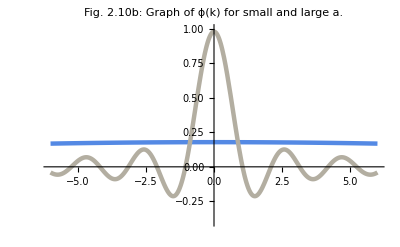

```mathematica
Plot[{ϕk /. {a -> 0.1}, ϕk /. {a -> 3}}, {k, -6, 6}, PlotRange -> {{-6, 6}, {-0.4, 1}}, PlotStyle -> {Thickness[0.008]}, PlotLabel -> "Fig. 2.10b: Graph of ϕ(k) for small and large a."]
```

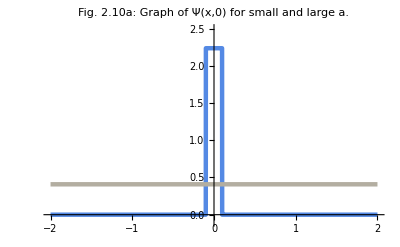

```mathematica
Plot[{Ψx0[x] /. {A -> NormSol26a /. {a -> 0.1}, a -> 0.1}, Ψx0[x] /. {A -> NormSol26a /. {a -> 3}, a -> 3}}, {x, -2, 2}, PlotRange -> {{-2, 2}, {-0.1, 2.5}}, ExclusionsStyle -> {{Red, Dashed}, Blue}, PlotStyle -> {Thickness[0.008]}, PlotLabel -> "Fig. 2.10a: Graph of Ψ(x,0) for small and large a."]
```

```mathematica
Finalmente volvemos a conectar esto en la ecuación 2.100:
```

```mathematica
Ψxt=1/(2π)^(1/2)*Integrate[ϕk E^(I( k x-ℏ/(2m) k^2)t),{k,-∞,∞},Assumptions->{x∈Reals, a∈Reals,k∈Reals,t>0,ℏ>0,m>0}]
```

((1/12+ⅈ/12) Abs[a-t x] Abs[a+t x] (6 ⅈ t (-a+t x) ℏ HypergeometricPFQ[{1/4},{1/2,5/4},-(m^2 (a-t x)^4)/(16 t^2 ℏ^2)]-6 ⅈ t (a+t x) ℏ HypergeometricPFQ[{1/4},{1/2,5/4},-(m^2 (a+t x)^4)/(16 t^2 ℏ^2)]+m ((a-t x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(m^2 (a-t x)^4)/(16 t^2 ℏ^2)]+(a+t x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(m^2 (a+t x)^4)/(16 t^2 ℏ^2)])))/(√(a/m) √(2 π) (t ℏ)^(3/2) Abs[a^2-t^2 x^2])

```mathematica
Ψxt /. {a -> 1., m -> 1, ℏ -> 1}
```

1/(t^(3/2) Abs[1.-t^2 x^2])(0.0332452+0.0332452 ⅈ) Abs[1.-t x] Abs[1.+t x] (6 ⅈ t (-1.+t x) HypergeometricPFQ[{1/4},{1/2,5/4},-(1.-t x)^4/(16 t^2)]-6 ⅈ t (1.+t x) HypergeometricPFQ[{1/4},{1/2,5/4},-(1.+t x)^4/(16 t^2)]+(1.-t x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(1.-t x)^4/(16 t^2)]+(1.+t x)^3 HypergeometricPFQ[{3/4},{3/2,7/4},-(1.+t x)^4/(16 t^2)])

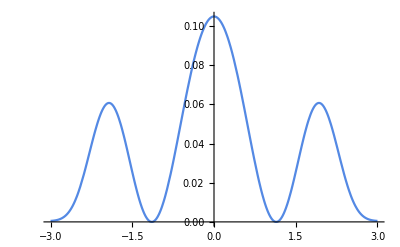

```mathematica
(*== Review ==*)
Plot[Im[Ψxt]^2/.{a->1.0,m->1,ℏ->1,t->1},{x,-3,3}]
```

Transformada de Fourier a cámara lenta.

```mathematica
f[t_]=(4/Pi) Sum[(1/n) Sin[2 Pi n t],{n,1,∞,2}]
f1[t_]=Sum[(1/n) Sin[2 Pi n t],{n,1,3,2}]
```

1/π 2 ⅈ (ArcTanh[ⅇ^(-2 ⅈ π t)]-ArcTanh[ⅇ^(2 ⅈ π t)])

Sin[2 π t]+1/3 Sin[6 π t]

```mathematica
El ArcTanh se puede transformar en funciones sinusoidales reales simples
```

```mathematica
E2T[t_]=Expand[(ExpToTrig[Sum[(ⅇ^(-2 ⅈ π t))^(2 n-1)/(2 n-1),{n,3}]]-ExpToTrig[Sum[(ⅇ^(2 ⅈ π t))^(2 n-1)/(2 n-1),{n,3}]])*I]
```

2 Sin[2 π t]+2/3 Sin[6 π t]+2/5 Sin[10 π t]

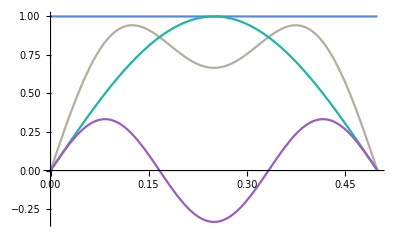

```mathematica
Plot[{f[t],f1[t],(1/n) Sin[2 Pi n t]/.{n->1},
(1/n) Sin[2 Pi n t]/.{n->3}},{t,0,0.5}]
```

Desafortunadamente, esta integral no puede ser resuelta en términos de funciones elementales, aunque, por supuesto, puede ser evaluada numéricamente (Figura 2.8).

```mathematica
[Buscar en algún momento integrales del tipo ∫ⅇ^(-(ax^2+bx))ⅆx]
```

```mathematica
(* == I put a -> 1=*)
(* == Tarda un poco .. como 6 mins ==*)
Ψxta=Integrate[E^(-I ℏ t/(2m)*(k-m/(ℏ t)x)^2),{k,-∞,∞},Assumptions->{x∈Reals, k∈Reals,t>0,ℏ>0,m>0}]
(*ΨxtaFin=1/(2π)E^(I m/(2ℏt)x^2)*Ψxta*)
(*Ψxta2=(Ψxta)^2*)
(* revisar luego == *)
```

(1-ⅈ) √π √(m/(t ℏ))

```mathematica
ΨxtaFin=1/(2π)E^(I m/(2ℏ t)x^2)*Ψxta/.{m->1,ℏ->1,t->2}
```

((1/2-ⅈ/2) ⅇ^((ⅈ x^2)/4))/(√(2 π))

```mathematica
Debería dar
```

```mathematica
ΨxtaFin2=Sqrt[1/(2π)]Sign[t]π/4 E^(I m/(2ℏ t)x^2)/.{m->1,ℏ->1,t->1.5}
```

1/4 ⅇ^((0.+0.333333 ⅈ) x^2) √(π/2)

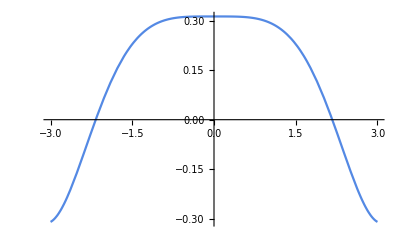

```mathematica
Plot[Re[ΨxtaFin2], {x, -3, 3}]
```

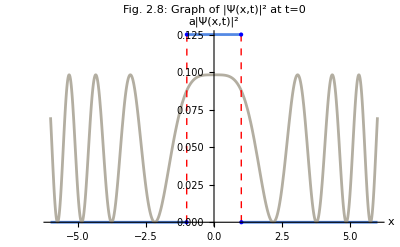

```mathematica
(* =================*)
(* == Ploting 2.8 == *)
Ψx0a[x_]:=Piecewise[{{A,-1≤x≤1},{0,True}}]/.{A->NormSol26a/.{a->1.0}}
(* ((Cos[x 0.8])^2/2 E^(-x^2/10)) ==  Inventada *)
(* == El super Plot ==*)
Plot[{(Ψx0a[x])^2,(Re[ΨxtaFin2])^2(* Todavia no se revisar *)},
{x,-6,6},
ExclusionsStyle->{{Red,Dashed},Blue},
PlotStyle->{Thickness@0.005},
LabelStyle->Directive[Black,25],
AxesLabel->{Style["x",24],Style["a|Ψ(x,t)|^2",24]},
PlotLabel->Style["Fig. 2.8: Graph of |Ψ(x,t)|^2 at t=0",18]]
```

Dos límites, a<<0 y a>>0 (el primero preciso en posición y gran dispersión en φ(k) o momento), el segundo (algún día trabajando en las Figs. 2.9 y 2.10)

ϕ(k) = (a/π)^(1/2)(sin(ka))/ka.

Buen impulso, pero posición mal definida.

El ψ_k(x,t) no es un estado físicamente realizable. La idea esencial es la siguiente: un paquete de ondas es una superposición de funciones sinusoidales cuya amplitud está modulada por φ. Consiste en "ondas" contenidas dentro de una "envoltura".

```mathematica
Algo de álgebra... (ver un día), y
```

Ψ(x,t) ≃ ⅇ^(-ⅈ(ω_0-k_0 ω'_0)t) Ψ(x-ω_0't,0)   (2.105)

```mathematica
Dónde
```

v_group = dω/dk    (2.106)

(evaluado en k=k_0). Esto debe contrastarse con la velocidad de fase ordinaria

```mathematica
Subíndice[v, fase] = ω/k (2.107)
```

v_phase = ω/k    (2.107)

Only missing the dispersion relation [ ω =(ℏk^2/(2m)) ], and comparing.

v_classical=v_group= 2v_phase.    (2.108)

```mathematica
Problemas 2.18-2.20(1)...
```

El potencial de la función delta

## Estados enlazados y estados de dispersión

```mathematica
La ecuación de Schrödinger tiene dos tipos de soluciones: estados ligados (pozo infinito), estados de dispersión (partícula libre). Suma (sobre n) e Integral (sobre k). ¿Cuál es la distinción?
```

## Representación gráfica de la Figura 2.12:

```mathematica
Estados consolidados
```

```mathematica
p212a=FindRoot[Cos[x]*E^(-x^2)-1x^3Sin[x^2]+6==5.5,{x,1}][[1]][[2]]
p212b=FindRoot[Cos[x]*E^(-x^2)-1x^3Sin[x^2]+6==5.5,{x,2}][[1]][[2]]
```

0.965835

1.74617

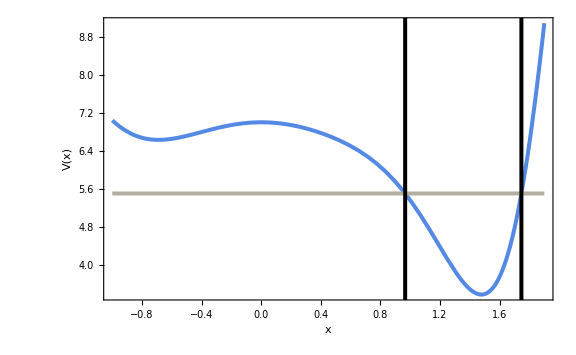

```mathematica
(* == ==*)
Plot[{Cos[x]*E^(-x^2)-1x^3Sin[x^2]+6,5.5},
{x,-1,1.9},
(* == Lineas Verticales == *)
Epilog->{Thickness@0.005,
Line[{{p212a,0},{p212a,36}}],Line[{{p212b,0},{p212b,36}}]},
(* ====================== *)
Frame->True,
PlotStyle->{Thickness@0.005},
LabelStyle->Directive[Black,25],
FrameLabel->{Style["x",24],Style["V(x)",24]
,Style["Fig. 2.12: (a) A bound state",24]},
FrameTicks->None,
ImageSize->Large]
```

{E<0  [V(-∞)  and V(∞)]⇒ bound state
E>0  [V(-∞)  or V(∞)]⇒ scattering state

```mathematica
en la vida real V - > 0 en ∞ , por lo que aún más
```

{E<0⇒ bound state
E>0⇒scattering state

## El pozo de la función delta

La función delta de Dirac es un pico infinitamente alto, infinitesimalmente estrecho en el origen, cuya área es 1.

δ(x)≡{0, if x≠0
∞, if x=0  with  ∫_(-∞)^(+∞) δ(x)ⅆx = 1   (2.111)

```mathematica
En particular
```

∫_(-∞)^(+∞) f(x)δ(x-a)ⅆx = f(a)   (2.113)

```mathematica
Consideremos un potencial de la forma
```

```mathematica
V(x) = -α δ(x), (2.114)
```

La ecuación de Schrödinger para el pozo de la función delta es la siguiente:

-ℏ^2/(2m)(d^2 ψ)/dx^2-αδ(x)ψ=E ψ .  (2.115)

```mathematica
Produce tanto E<0 como E>0.
```

```mathematica
WriteHv1[-αδ[x]][ψ[x]] == E1 ψ[x]
```

-ℏ^2/(2 m) (∂^2 ψ(x))/(∂x^2)+-αδ(x) ψ(x)==E1 ψ[x]

Primero x<0, V(x)=0, por lo que

```mathematica
(EqD25 = WriteHv1[0][ψ[x]] == E1 ψ[x]) (EqD25a = hamiltonian[0][ψ[x]] == E1 ψ[x])
```

-ℏ^2/(2 m) (∂^2 ψ(x))/(∂x^2)==E1 ψ[x]

-(ℏ^2 ψ''[x])/(2 m)==E1 ψ[x]

```mathematica
DSolve[D[y[x], {x, 2}] == y[x], y, x]
```

{{y→Function[{x},ⅇ^x C[1]+ⅇ^-x C[2]]}}

```mathematica
EqD25aSol = DSolve[EqD25a, ψ, x]
```

{{ψ→Function[{x},C[1] Cos[(√2 √E1 √m x)/ℏ]+C[2] Sin[(√2 √E1 √m x)/ℏ]]}}

```mathematica
(* == Some day see, but look at above, it was good ==*)
EqD25aSol=DSolve[EqD25a,ψ,x]
```

{{ψ→Function[{x},C[1] Cos[(√2 √E1 √m x)/ℏ]+C[2] Sin[(√2 √E1 √m x)/ℏ]]}}

```mathematica
Mejor, E<0 por suposición, k es Real.
```

(d^2 ψ)/dx^2=k^2ψ,   with  k= (- 2mE)^(1/2)/ℏ   (2.116)

La solución general de la ecuación 2.116 es

ψ(x) = Aⅇ^-kx + Bⅇ^kx,  (2.118)

```mathematica
Pero, el primer término -> ∞ como x -> -∞, luego A=0, y
```

ψ(x) = Bⅇ^kx, (x<0) (2.119)

```mathematica
En la región x>0, ...
```

ψ(x) = Fⅇ^-kx, (x>0) (2,119)

```mathematica
Las condiciones de contorno estándar para ψ:
```

1. ψ es siempre continuo
2. dψ/dx es continuo, excepto en los puntos 
donde el potencial es ∞.

```mathematica
El primero nos dice que F = B, por lo que
```

ψ(x) =  {B ⅇ^kx, (x≤0),
B ⅇ^-kx, (x≥0),   (2.122)

```mathematica
Trazando rápido,
```

```mathematica
ψD25a[x_]:=Piecewise[{{ⅇ^x,x≤0},{ⅇ^-x,x≥0}}]
```

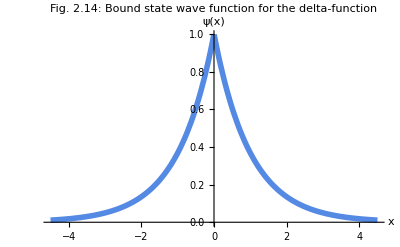

```mathematica
Plot[ψD25a[x],{x,-4.5,4.5},
PlotStyle->{Thickness@0.01},
LabelStyle->Directive[Black,22],
AxesLabel->{Style["x",24],Style["ψ(x)",24]},
PlotLabel->Style["Fig. 2.14: Bound state wave function \n for the delta-function",18]]
```

La función delta debe determinar la discontinuidad en la derivada de ψ, en x=0.

```mathematica
Debido a 2.113, (recuerde el truco ε y los límites ⟶ 0), la última integral es cero, y
```

Δ(dψ/dx) = -(2mα)/ℏ^2 ψ(0).    (2.125)

```mathematica
Desde 2.122
```

```mathematica
Δ(dψ/dx) = -2 B k.
```

Y ψ(0)=B. Así que 2.125 es

κ = mα/ℏ^2 ,   (2.126)

```mathematica
y la energía permitida es
```

E = -mα^2/(2 ℏ^2) ,   (2.127)

```mathematica
Finalmente normalizamos
```

```mathematica
κ = mα/ħ^2 , (2.126)
```

```mathematica
ψD25b[x_]:=B ⅇ^(-k Abs[x])
```

```mathematica
(* == The Assumptions is key !! == nice to do it like that ==*)
Integrate[2(ψD25b[x])^2,{x,0,∞},Assumptions->{x∈Reals, k∈Reals,B∈Reals}]
```

Piecewise[{{B^2/k, k>0}, {B^2 ∞, True}}]

```mathematica
NormaDel25=Integrate[2(ψD25b[x])^2,{x,0,∞},Assumptions->{x∈Reals, k∈Reals,B∈Reals}]==1
(* hay que igualar dos veces porque al agarrar el valor ..*)
Solve[NormaDel25[[1]][[1]][[1]][[1]]==1,B]
```

(Piecewise[{{B^2/k, k>0}, {B^2 ∞, True}}])==1

{{B→-√k},{B→√k}}

```mathematica
B = √k
```

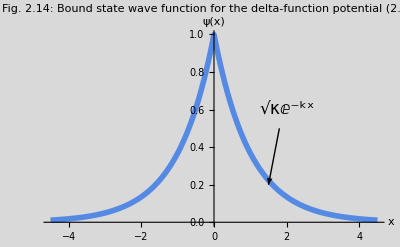

```mathematica
pl1214a=Plot[ψD25b[x]/.{B->1,k->1},{x,-4.5,4.5},
PlotStyle->{Thickness@0.01},
LabelStyle->Directive[Black,25],
AxesLabel->{Style["x",24],Style["ψ(x)",24]},
PlotLabel->Style["Fig. 2.14: Bound state wave function 
for the delta-function potential (2.122)",18],
Background->LightGray];
(* Labels with Arrows V1.0 ==*)
lab1=Graphics[{Text[Style["√κⅇ^-kx",17],{2,0.6}],Arrow[{{1.8,0.5},{1.5,0.2}}]}];
(* ==========================*)
Show[{pl1214a,lab1}]
```

```mathematica
Evidentemente, el pozo de la función delta, independientemente de su α de "fuerza", tiene exactamente UN estado ligado:
```

ψ(x) = (√mα)/ℏ ⅇ^(-mα|x|/ℏ^2)  ;  E = - mα^2/(2 ℏ^2).   (2.129)

```mathematica
¡Gran conclusión!
```

```mathematica
¿Qué pasa con los estados de dispersión, con E > 0?, para x < 0 :
```

(d^2 ψ)/dx^2=-k^2ψ,   with  k= (2mE)^(1/2)/ℏ   (2.130)

k es real y positivo. La solución general es

ψ(x) = Aⅇ^ⅈkx + Bⅇ^-ⅈkx, (2.131)

Y esta vez no podemos descartar ninguno de los dos términos, ya que ninguno de los dos explota. Para x > 0:

```mathematica
ψ(x) = Fⅇ^ⅈkx + Gⅇ^-ⅈkx.     (2.132)
```

La continuidad de ψ(x) en x=0 requiere que

F + G = A + B.  (2.133)

ⅈκ(F-G-A+B) = - (2mα)/ℏ^2(A+B),   (2.134)

```mathematica
o más compactamente... Tenemos que pensar,
```

```mathematica
En un experimento de dispersión típico, las partículas se disparan desde una dirección. G = 0.  A = Onda incidente, B = Onda reflejada, F = Onda transmitida.
```

```mathematica
B = ⅈβ/(1-ⅈβ) A, F = 1/(1-ⅈβ) A.   (2.137)
```

con β=(mα)/(ħ^2 κ).

R ≡ (|B|^2)/(|A|^2) = β^2/(1+β^2) . (2.138)

Para representar este coeficiente

```mathematica
ReCoef =1/(1+(2 ℏ^2 Ene/(m α^2)))
```

1/(1+(2 Ene ℏ^2)/(m α^2))

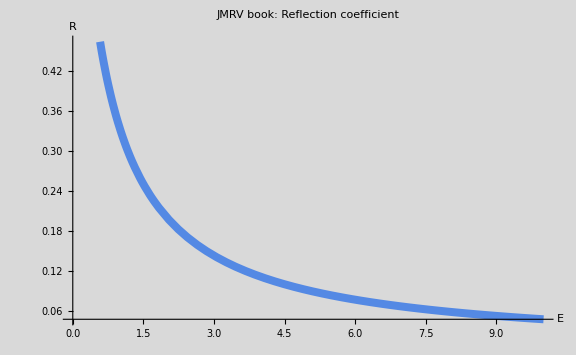

```mathematica
plRCoef1=Plot[ReCoef/.{ℏ->1,m->1,α->1},{Ene,0,10},
PlotStyle->{Thickness@0.01},
LabelStyle->Directive[Black,25],
AxesLabel->{Style["E",24],Style["R",24]},
PlotLabel->Style["JMRV book: Reflection coefficient",18],
Background->LightGray,ImageSize->Large]
(* ==========================*)
```

```mathematica
R se denomina coeficiente de reflexión. La probabilidad de transmisión viene dada por el coeficiente de transmisión (¡compruébalo!)
```

T ≡ (|F|^2)/(|A|^2) = 1/(1+β^2) . (2.139)

Para representar este coeficiente

```mathematica
TrCoef =1/(1+(2 ℏ^2 Ene/(m α^2))^-1)
```

1/(1+(m α^2)/(2 Ene ℏ^2))

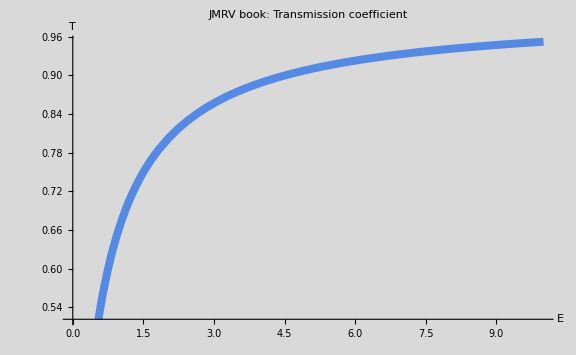

```mathematica
plTCoef1=Plot[TrCoef/.{ℏ->1,m->1,α->1},{Ene,0,10},
PlotStyle->{Thickness@0.01},
LabelStyle->Directive[Black,25],
AxesLabel->{Style["E",24],Style["T",24]},
PlotLabel->Style["JMRV book: Transmission coefficient",18],
Background->LightGray,ImageSize->Large]
(* ==========================*)
```

```mathematica
Por supuesto, la suma tiene que ser 1:
```

```mathematica
R + T = 1.   (2.140)
```

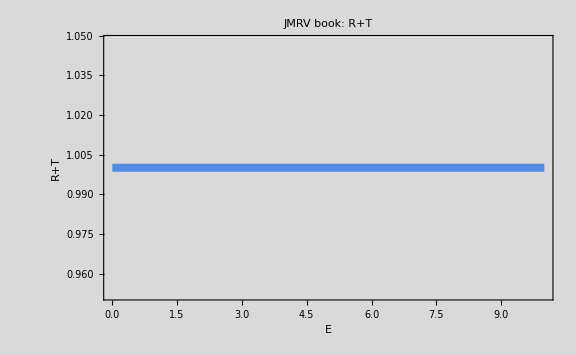

```mathematica
plTotal1=Plot[(ReCoef+TrCoef)/.{ℏ->1,m->1,α->1},{Ene,0,10},
Frame->True,
PlotStyle->{Thickness@0.01},
LabelStyle->Directive[Black,25],
AxesLabel->{Style["E",24],Style["R+T",24]},
PlotLabel->Style["JMRV book: R+T",18],
Background->LightGray,ImageSize->Large]
(* ==========================*)
```

Con este sencillo código, estoy tratando de ejemplificar sobre el perfil espacial de viaje.

```mathematica
(* == No usado, pero dejar por aqui == for JMRV book *)
Animate[Plot[Exp[-(x+2-t)^2],{x,-2,2},PlotRange->{0,1}],{t,0,5,0.2}]
```

```mathematica
(* == No usado, pero dejar por aqui == for JMRV book *)
f[x_,t_]:=Cos[x+t]+Cos[1.2 x+1.2t];Animate[Plot[f[x,t],{x,-16,16},PlotRange->{-2.5,2.5}],{t,0,30,1}]
```

Pozo infinito -- Libro de JMRV

```mathematica
psi[x_,t_,n_]:=Sum[a[j] Sin[j Pi x] Exp[-I Pi j^2t],{j,1,n-1}]+Sqrt[1-Sum[a[m]^2,{m,1,n-1}]] Sin[n Pi x]Exp[-I Pi n^2 t];
p[x_,t_,n_]:=ComplexExpand[psi[x,t,n] Conjugate[psi[x,t,n]]]
(* all constants to 1 *)
a[1]:=1/Sqrt[2];
Animate[Plot[p[x,t,2],{x,0,1}],{t,0,2Pi/3,0.05}]
```

Continúe con la función Delta.

```mathematica
Bueno, toda la discusión en la página 76. Si E < Subíndice[V, máx.] clásicamente, rebotan, en mecánica cuántica la probabilidad (T ≠ 0). Esto es lo que llamamos tunelización. Toda la electrónica moderna y la microcopia.
```

Problemas ...

El pozo cuadrado finito

```mathematica
Como último ejemplo, considere el potencial del pozo cuadrado finito
```

V(x)={-V_0,               for -a<x<a,
0, for|x|>a,(2.145)

Donde Subíndice[V, 0] es una constante (positiva) (ver Fig. 2.17)

## Representación gráfica de la Figura 2.17

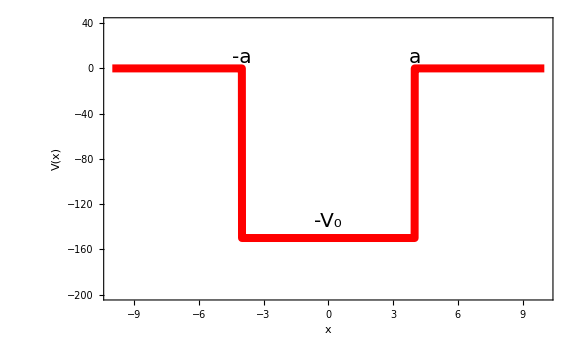

```mathematica
a=4.0;
V0=150.0;
V[x_]:=Which[x<-a,0,-a≤x≤a,-V0,a<x,0]
pl1217a=Plot[V[x],{x,-10,10},
Frame->True,
FrameLabel->{"x","V(x)",
Style["Fig. 2.17: The finite square well \n Equation (2.145)",18]},
FrameStyle->Black,
PlotRange->{{-10,10},{-200,40}},
Exclusions->None,
PlotStyle->{Thickness@0.01,Red},
LabelStyle->Directive[Black,25],
ImageSize->Large];
(* ==========================*)
(* Labels with Arrows V1.0 ==*)
lab1=Graphics[{
Text[Style["-a",20],{-a,10.}],
Text[Style["a",20],{a,10.}],
Text[Style["-V_0",20],{0,-V0+V0*0.1}]}];
(* ==========================*)
Show[{pl1217a,lab1}]
```

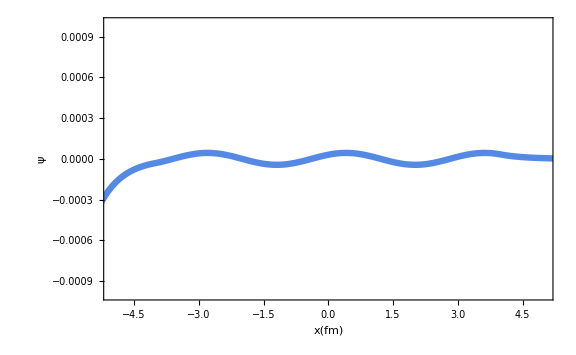

```mathematica
(* constants and parameters *)
hbarc = 197.0;
mc2   = 931.5;
A       = -(2*mc2)/hbarc^2;
Energy = -70;
xmin = -10;
xmax= 10;
(* numerical solution of DE. *)
sol=NDSolve[ {psi''[x] + A*(V[x] - Energy)*psi[x] == 0, psi[xmax] == 0.5, psi'[xmax] == 0.001},psi, {x,xmin,xmax}];
(* wave function normalization factor. *)
norm=1/(√NIntegrate[Evaluate[ psi[x]*psi[x] /. sol],{x,xmin,xmax}]);
(* Make a plot. *)
p1=Plot[Evaluate[ norm*psi[x] /. sol],{x,xmin,xmax},
       Frame->True,FrameLabel->{"x(fm)", "ψ",StringForm["E=`` MeV",NumberForm[Energy,20]], " "},
       FrameStyle->Black,PlotStyle->{Thickness@0.008},
PlotRange->{{-5,5},{-0.001,0.001}},
BaseStyle->FontSize->16, 
ImageSize->Large
      ]
```

Al igual que la función delta, el pozo cuadrado admite los estados Enlazado (E<0) y Dispersión (E>0).

### Estados de límites (E<0)

```mathematica
Veremos primero los estados ligados. En la región x < -a, el potencial es cero y
```

(d^2 ψ)/dx^2=k^2ψ,   with  k= (- 2mE)^(1/2)/ℏ   (2.146)

k es real y positivo. La solución físicamente admisible es

ψ(x) = Bⅇ^kx, (x < -a) (2.147)

En la región -a < x < a, V(x)=-Subíndice[V, 0], la ecuación de Schrödinger se lee

```mathematica
(* == V = -V0 ==*)
EqFW26=WriteH1v1[-Subscript[V, 0]]@ψ[x]==E1*ψ[x](* para ver *)
EqFW26a=hamiltonian[-Subscript[V, 0]]@ψ[x]==E1*ψ[x] (* para resolver *)
```

-ℏ^2/(2 m) (∂^2 ψ(x))/(∂x^2)+-V_0 ψ(x)==E1 ψ[x]

-V_0 ψ[x]-(ℏ^2 ψ''[x])/(2 m)==E1 ψ[x]

```mathematica
O
```

(d^2 ψ)/dx^2=-ℓ^2ψ,   with  ℓ= [ 2m(E+V_0)]^(1/2)/ℏ   (2.148)

```mathematica
Aunque E es negativo, para los estados ligados, debe ser mayor que -Subíndice[V, 0], según el antiguo teorema E>Subíndice[V, min]; Así que l también es un número positivo real. La solución general es
```

ψ(x) = C sin(lx)+D cos(lx),  
para -a < x < a, (2.149)

```mathematica
EqFW26Bound=ψ''[x]==-ℓ^2 ψ[x]
DSolve[EqFW26Bound,ψ,x]
```

ψ''[x]==-ℓ^2 ψ[x]

{{ψ→Function[{x},C[1] Cos[x ℓ]+C[2] Sin[x ℓ]]}}

```mathematica
Donde C y D son constantes arbitrarias. Finalmente, en la región x>a, el potencial vuelve a ser cero; la solución general es ψ(x)=F exp(-kx)+G exp(kx), pero el segundo término explota como x ⟶ ∞, por lo que nos quedamos con
```

ψ(x) = F ⅇ^-kx, (x>a) (2,150)

```mathematica
El siguiente paso es imponer condiciones de contorno: ψ y dψ/dx continuas en -a y +a. (imponiendo solo en un lado, incluso por ejemplo). Elaboramos las soluciones uniformes; El coseno es parejo, por lo que estamos buscando soluciones de la forma
```

ψ(x) = 	{F ⅇ^-kx | for x> a, | 
D cos(ℓx) | 0<x< a, | 
ψ(-x) | for x< 0, |   (2.151)

La continuidad de ψ(x), en x=a dice

```mathematica
F ⅇ^-ka = D cos(la), (2.152)
```

```mathematica
Y la continuidad de dψ(x)/dx dice
```

-kF ⅇ^-ka = -ℓ D sin(ℓa),    (2.153)

Dividiendo (2.153) por (2.152), encontramos que

κ = l tan(la).     (2.154)

```mathematica
Esta es una fórmula para las energías permitidas, ya que κ y l son funciones de E. Para resolver E, primero adoptamos una notación más agradable:
```

z ≡ la, y Subíndice[z, 0] ≡ a/ħ√2 Subíndice[mV, 0] .    (2.155)

```mathematica
De acuerdo con (2.146) y (2.148), (κ^2 + l^2) = 2Subíndice[mV, 0]/ħ^2, por lo que ka=√Subíndice[z, 0]^2-z^2, y la ecuación 2.154 se lee
```

tangente z = √(z_0/z)-1.   (2.156)

## Representación gráfica de la Figura 2.18

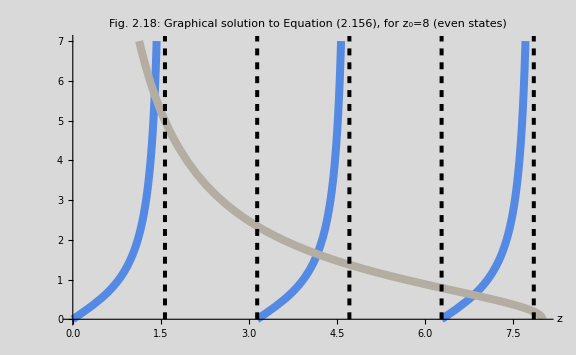

```mathematica
Subscript[z, 0]=8;(* even states *)
tanFig218a=Tan[x];
tanFig218b=Sqrt[(Subscript[z, 0]/x)^2-1];
Plot[{tanFig218a,tanFig218b},{x,0,Subscript[z, 0]+0.02},
PlotRange->{0,7},
(* == Lineas Verticales == *)
Epilog->{Thickness@0.005,Dashed,
Line[{{π/2,0},{π/2,36}}],
Line[{{π,0},{π,36}}],
Line[{{3π/2,0},{3π/2,36}}],
Line[{{2π,0},{2π,36}}],
Line[{{5π/2,0},{5π/2,36}}]},
(* ====================== *)
PlotStyle->{Thickness@0.01},
LabelStyle->Directive[Black,25],
AxesLabel->{Style["z",24],""},
PlotLabel->Style["Fig. 2.18: Graphical solution to Equation
(2.156), for z_0=8 (even states)",18],
Background->LightGray,
ImageSize->Large]
```

```mathematica
Numéricamente:
```

```mathematica
Do[
Roots2156a=FindRoot[tanFig218a==tanFig218b,{x,i}];
Print[Roots2156a];,
{i,1,Subscript[z, 0]-1}]
```

Dos casos limitantes:

1. Pozo amplio y profundo. Si el subíndice [z, 0] es muy grande, las intersecciones se producen ligeramente debajo de cada subíndice [z, n]=n π/2, con n impar y:

E_n + V_0 ≃ (n^2 π^2 ℏ^2)/(2(m(2a))^2).  (2.157)

Pero, E+Subíndice[V, 0] es la energía por encima del fondo del pozo, y en el lado derecho [de 2.157] tenemos precisamente las infinitas energías cuadradas del pozo, para un pozo de ancho 2a! Por lo tanto, el pozo del cuadrado infinito pasa al pozo del cuadrado infinito, como Subíndice[V, 0] ⟶ ∞ (véase 2.155); sin embargo, para cualquier subíndice finito [V, 0] solo hay un número finito de estados enlazados.

```mathematica
2. Pozo poco profundo y estrecho. A medida que el subíndice [z, 0] disminuye (⟶ 0), hay cada vez menos estados enlazados, hasta que finalmente (para el subíndice [z, 0] < π/2, donde desaparece el estado impar más bajo) solo queda UNO. Es interesante notar, sin embargo, que siempre hay UN estado limitado, no importa cuán "débil" se vuelva el pozo.
```

```mathematica
Visualmente esta conclusión es:
```

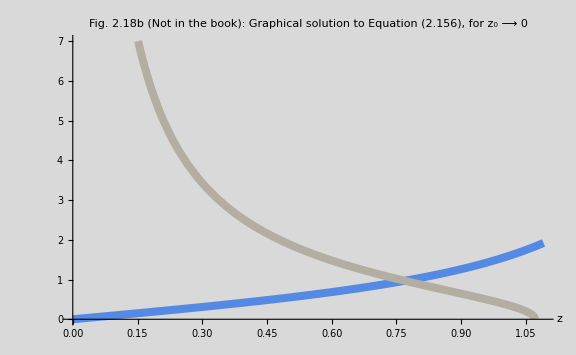

```mathematica
Subscript[z, 0]=π/2-0.5;(* For the limiting case Subscript[z, 0] ⟶ 0 *)
tanFig218a=Tan[x];
tanFig218b=Sqrt[(Subscript[z, 0]/x)^2-1];
Plot[{tanFig218a,tanFig218b},{x,0,Subscript[z, 0]+0.02},
PlotRange->{0,7},
(* == Lineas Verticales == *)
Epilog->{Thickness@0.005,Dashed,
Line[{{π/2,0},{π/2,36}}],
Line[{{π,0},{π,36}}],
Line[{{3π/2,0},{3π/2,36}}],
Line[{{2π,0},{2π,36}}],
Line[{{5π/2,0},{5π/2,36}}]},
(* ====================== *)
PlotStyle->{Thickness@0.01},
LabelStyle->Directive[Black,25],
AxesLabel->{Style["z",24],""},
PlotLabel->Style["Fig. 2.18b (Not in the book): Graphical solution
 to Equation (2.156), for z_0 ⟶ 0",18],
Background->LightGray,
ImageSize->Large]
```

### Estados de dispersión E>0

Le invitamos a normalizar (2.151). Pero vamos a pasar ahora a los estados de DISPERSIÓN (E>0). A la izquierda, donde V(x)=0, tenemos:

ψ(x) = A ⅇ^ⅈkx + B ⅇ^-ⅈkx, for (x< -a)     (2.158)

donde κ ≡ (√2 m E)/ħ (2.159).

```mathematica
Dentro del pozo, donde V(x)=-Subíndice[V, 0],
```

```mathematica
ψ(x) = C sin(lx)+D cos(lx),  
para -a < x < a, (2.160)
```

as before  ℓ= [ 2m(E+V_0)]^(1/2)/ℏ   (2.161)

A la derecha, suponiendo que no haya una ola entrante en esta región, tenemos

ψ(x) = F ⅇ^-ⅈkx, (2.162)

```mathematica
Aquí A es la amplitud incidente, B es la amplitud reflejada y F es la amplitud transmitida.
```

Vuelva a aplicar las condiciones de los límites y resuelva B y F:

B =ⅈ (sin(2ℓa))/(2kℓ) (ℓ^2- k^2) F,   (2.167)

F =   (ⅇ^(-2ⅈka)A)/(cos(2ℓa) -ⅈ (k^2+ℓ^2)/(2kℓ)sin(2ℓa)).  (2.168)

```mathematica
El coeficiente de transmisión T = |F(|^2) / |A(|^2), expresado en términos de las variables originales, viene dado por
```

T^-1=1+V_0^2/(4E(E+V_0)) sin^2((2a)/ℏ√(2m(E+V_0))).  (2.169)

```mathematica
Nótese que T = 1 (el pozo se vuelve "transparente") siempre que el seno sea cero, es decir, cuando
```

((2a)/ℏ  √(2m(E+V_0)) ) = nπ.  (2.170)

## Representación gráfica de la Figura 2.19:

```mathematica
TFig219=(1+Subscript[V, 0]^2/(4E1(E1+Subscript[V, 0]))(Sin[(2a)/ℏ(2m(E1+Subscript[V, 0]))^(1/2)])^2)^-1
```

1/(1+(Sin[(2 √2 a √(m (E1+V_0)))/ℏ]^2 V_0^2)/(4 E1 (E1+V_0)))

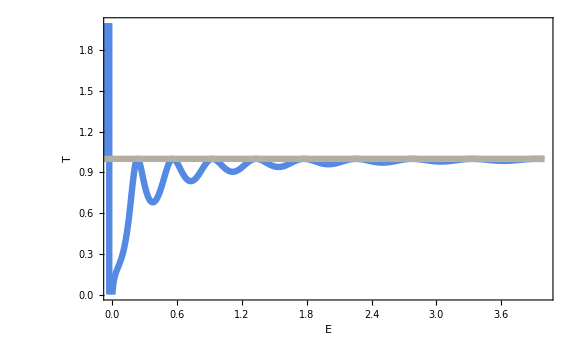

```mathematica
pl1219a=Plot[{TFig219/.{a->8,Subscript[V, 0]->1,ℏ->1,m->1},1},{E1,-1,4},
Frame->True,
FrameLabel->{"E","T",
Style["Fig. 2.19: Transmission coefficient as a 
function of energy (2.169)",22]},
FrameStyle->Black,
PlotRange->{{0,4},{0,2}},
Exclusions->None,
PlotStyle->{Thickness@0.008},
LabelStyle->Directive[Black,25],
ImageSize->Large]
```

```mathematica
Las energías para la transmisión perfecta, entonces, están dadas por
```

E_n + V_0 =   (n^2 π^2 ℏ^2)/(2(m(2a))^2),  (2.171)

```mathematica
que resultan ser precisamente las energías permitidas para el pozo infinito (∞) cuadrado.
```

```mathematica
Problemas 2.29-2.33 ...
```